```mathematica
FileNameForGoodValue[ primes_] := Module[{fileName, temp, sep, p, pPos},
sep = "\\";
temp ="d:\\triangle\DataSrc";
For[pPos =1, pPos <= Length[primes], pPos++,
temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
];
temp = StringJoin[temp, "\\Solutions.txt"];
fileName = temp;
Return[fileName]
]
```

```mathematica
GoodValuesFor [primes_] := ReadList[FileNameForGoodValue[primes],Number]
```

```mathematica
StepFunction[list_, x_] := 
Length[
Select[list, # < x&]
]
```

```mathematica
ExpectedGraham[tuple_, x_] := x^(1+ Sum[ Log[(p+1)/(2*p)] / Log[p],{p, tuple}])
```

```mathematica
good=Select[GoodValuesFor[{7,11,13,19}], # ≤ 10^8&]
```

{0,1,2,3,57,58,364,365,366,367,407,408,2915,36179,36183,36184}

```mathematica
stepGood[x_]:= stepGood[x]=If [x==0,0, If [MemberQ[good,x],1,0] + stepGood[x-1]]
```

```mathematica
Clear[stepGood]
```

```mathematica
With[{tuple={7,11,13,19},
range=10^8},
With [{
good=Select[GoodValuesFor[tuple], # ≤ range&]},
Show[
(*LogPlot[
Product[ Log[((p+1)/2p )]^(Log[x]/ Log[p]), {p,tuple}],
{x,0,10^2}
],*)
ListPlot[Table[stepGood[x], {x,1,range}]
],
ListPlot[Table[ExpectedGraham[tuple,x], {x,1,range}],
PlotStyle->Green]
]
]
]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

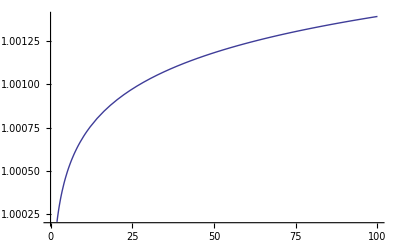

```mathematica
With[{tuple={7,11,13,19}},
Show[
Plot[
ExpectedGraham[tuple,x],
{x,0,10^2}
]

]
]
```

```mathematica
With[{tuple={7,11,13,17},
good=GoodValuesFor[{7,11,13,19}]},
(*LogPlot[
Product[ ((p+1)/2p )^(Log[x]/ Log[p]), {p,tuple}],
{x,0,10^10}
],*)
Table[Length[
Select[good, # < x&]
], {x,0,10^2}
]
]
```

{0,1,2,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

```mathematica
N[ExpectedGraham[{23,37,43,47}, 10^20]]
```

127033.